```mathematica
(*
A set of person are given the same money at the begnning;
Each round, they give another person 1$ randomly;
*)
```

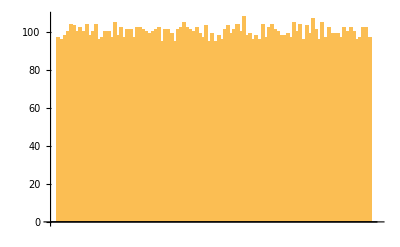

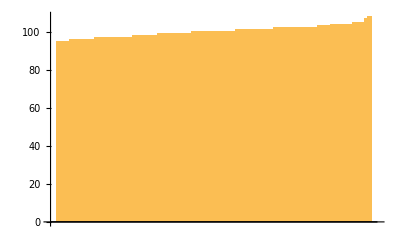

```mathematica
(*Exchange 10 times*)
Nn =100;
InitMon =100;
Time = 10;

MonList=Table[InitMon,{i,1,Nn}];
c =0;

For[ii=1,ii≤Time,ii++,
For[jj=1,jj≤Nn,jj++,
MonList[[jj]]--;
GetRn=RandomInteger[{1,Nn}];
While[GetRn<1||GetRn>Nn,GetRn=RandomInteger[{1,Nn}];];
MonList[[GetRn]]++;
];
];
BarChart[MonList]
BarChart[Sort[MonList],PlotRange->All]
```

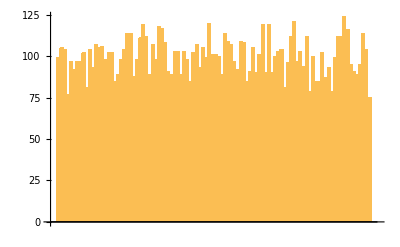

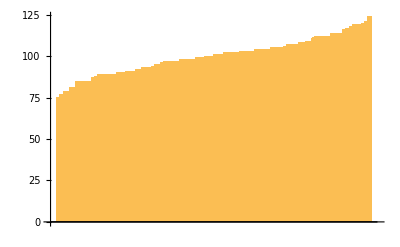

```mathematica
(*Exchange 100 times*)
Nn =100;
InitMon =100;
Time = 100;

MonList=Table[InitMon,{i,1,Nn}];
c =0;

For[ii=1,ii≤Time,ii++,
For[jj=1,jj≤Nn,jj++,
MonList[[jj]]--;
GetRn=RandomInteger[{1,Nn}];
While[GetRn<1||GetRn>Nn,GetRn=RandomInteger[{1,Nn}];];
MonList[[GetRn]]++;
];
];
BarChart[MonList]
BarChart[Sort[MonList],PlotRange->All]
```

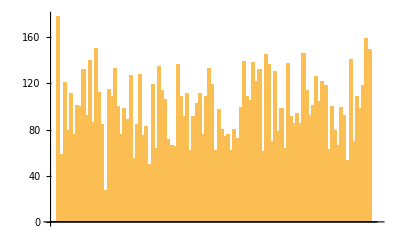

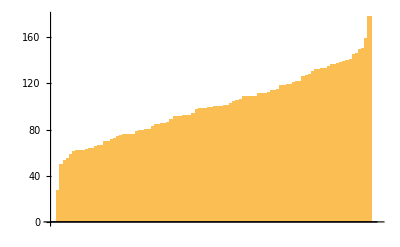

```mathematica
(*Exchange 1000 times*)
Nn =100;
InitMon =100;
Time = 1000;

MonList=Table[InitMon,{i,1,Nn}];
c =0;

For[ii=1,ii≤Time,ii++,
For[jj=1,jj≤Nn,jj++,
MonList[[jj]]--;
GetRn=RandomInteger[{1,Nn}];
While[GetRn<1||GetRn>Nn,GetRn=RandomInteger[{1,Nn}];];
MonList[[GetRn]]++;
];
];
BarChart[MonList]
BarChart[Sort[MonList],PlotRange->All]
```

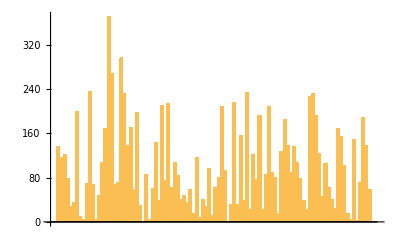

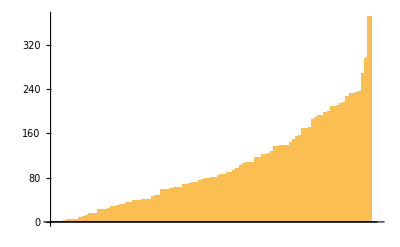

```mathematica
(*Exchange 10000 times*)
Nn =100;
InitMon =100;
Time = 10000;

MonList=Table[InitMon,{i,1,Nn}];
c =0;

For[ii=1,ii≤Time,ii++,
For[jj=1,jj≤Nn,jj++,
If[MonList[[jj]]≥0,
MonList[[jj]]--;
GetRn=RandomInteger[{1,Nn}];
While[GetRn<1||GetRn>Nn,GetRn=RandomInteger[{1,Nn}];];
MonList[[GetRn]]++;
];
];
];
BarChart[MonList]
BarChart[Sort[MonList],PlotRange->All]
```

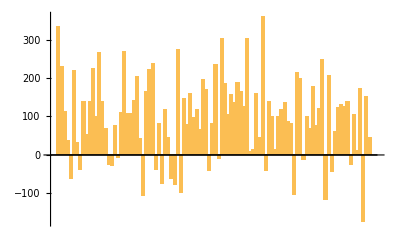

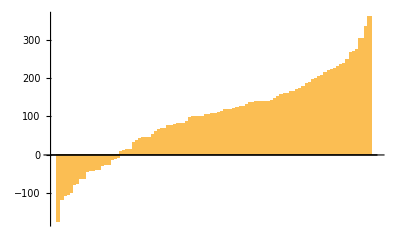

```mathematica
(*Exchange 1000 times*)
Nn =100;
InitMon =100;
Time = 10000;

MonList=Table[InitMon,{i,1,Nn}];
c =0;

For[ii=1,ii≤Time,ii++,
For[jj=1,jj≤Nn,jj++,
MonList[[jj]]--;
GetRn=RandomInteger[{1,Nn}];
While[GetRn<1||GetRn>Nn,GetRn=RandomInteger[{1,Nn}];];
MonList[[GetRn]]++;
];
];
BarChart[MonList]
BarChart[Sort[MonList],PlotRange->All]
```